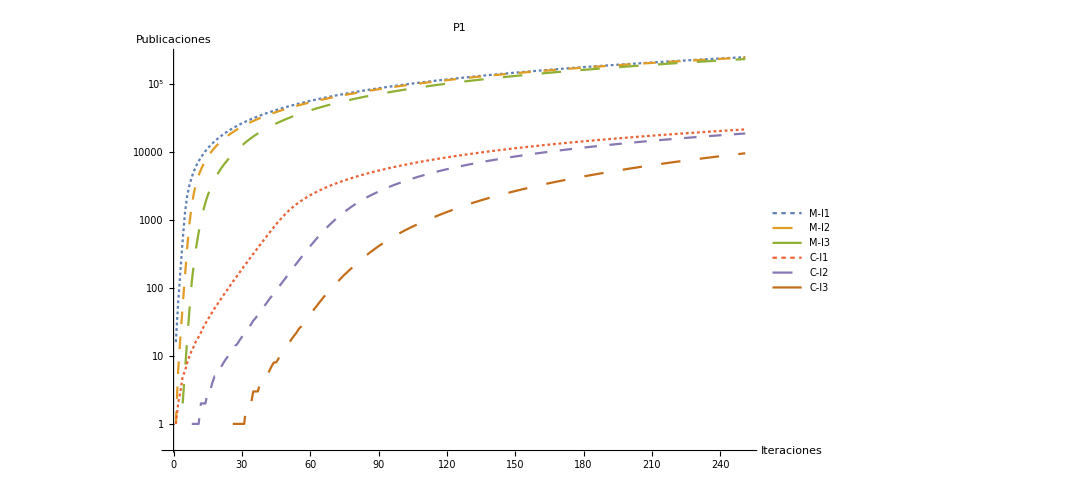
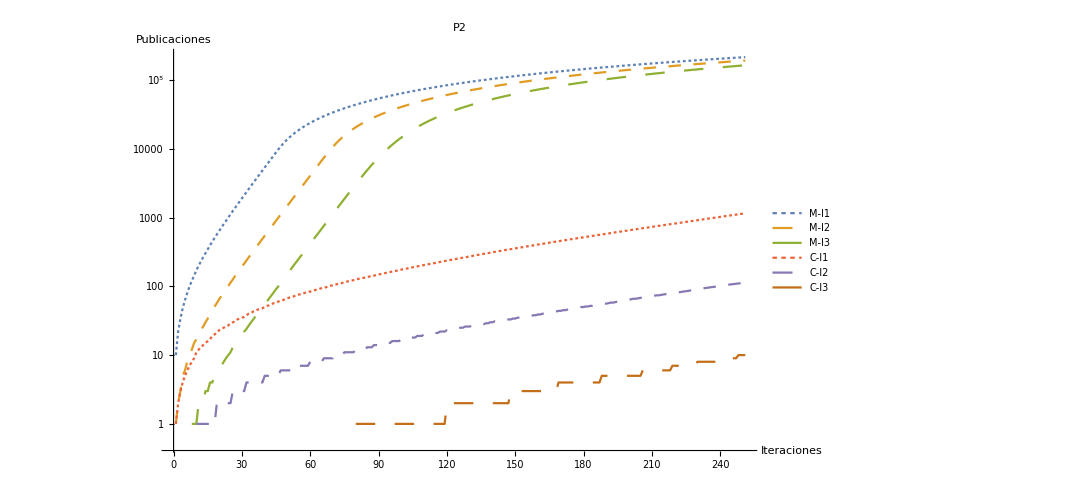
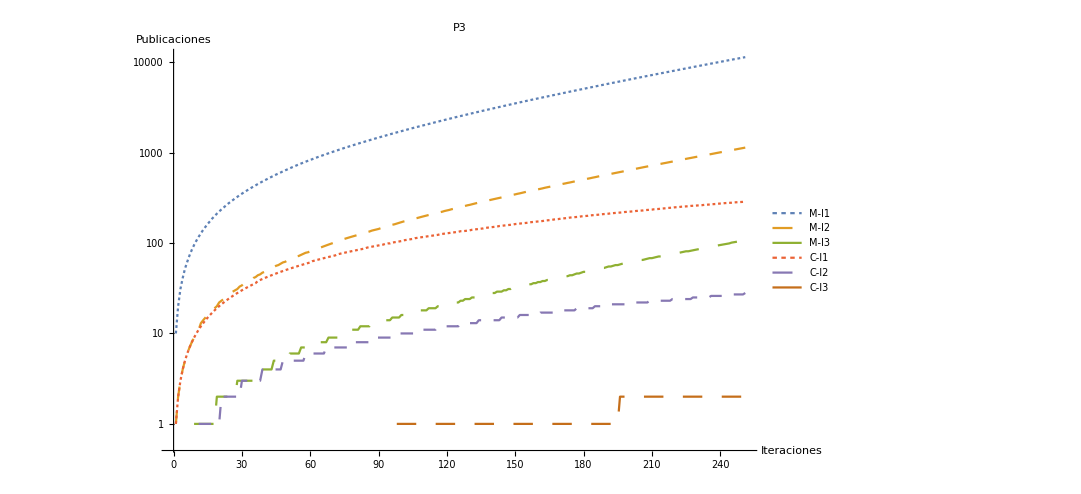
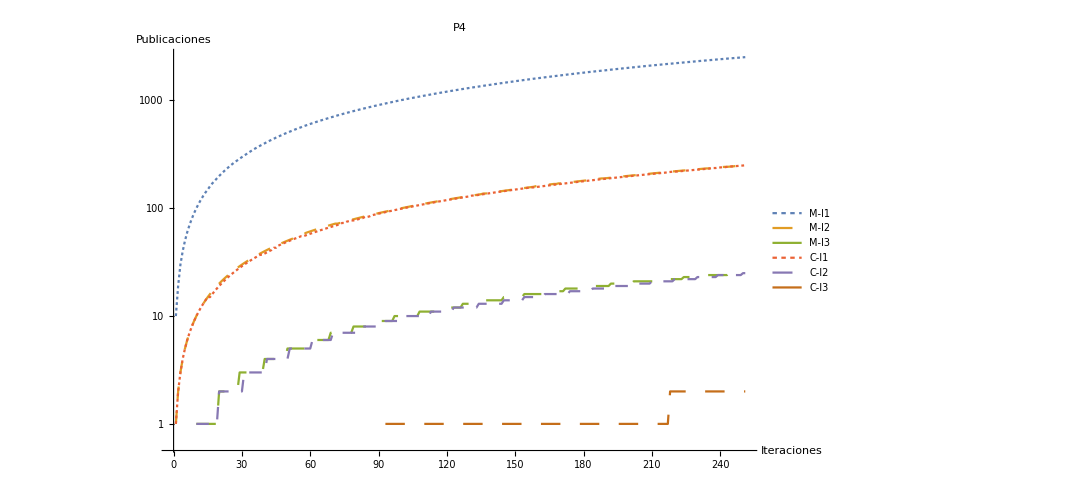
-Graphics- | -Graphics-
-Graphics- | -Graphics-

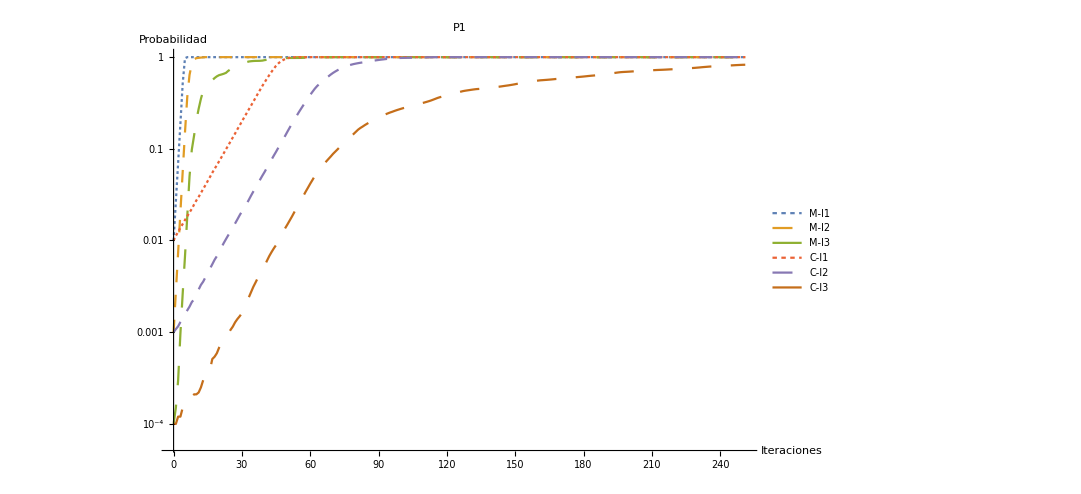
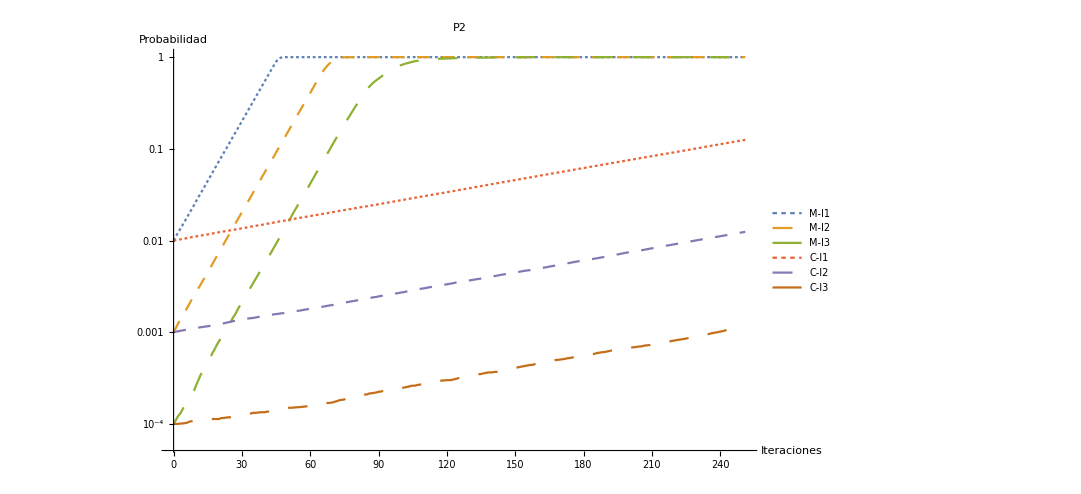
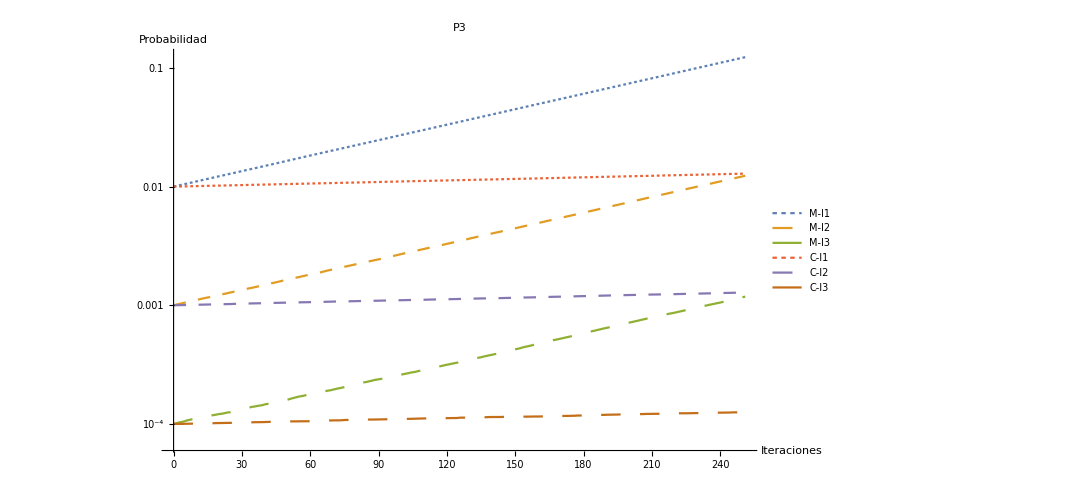
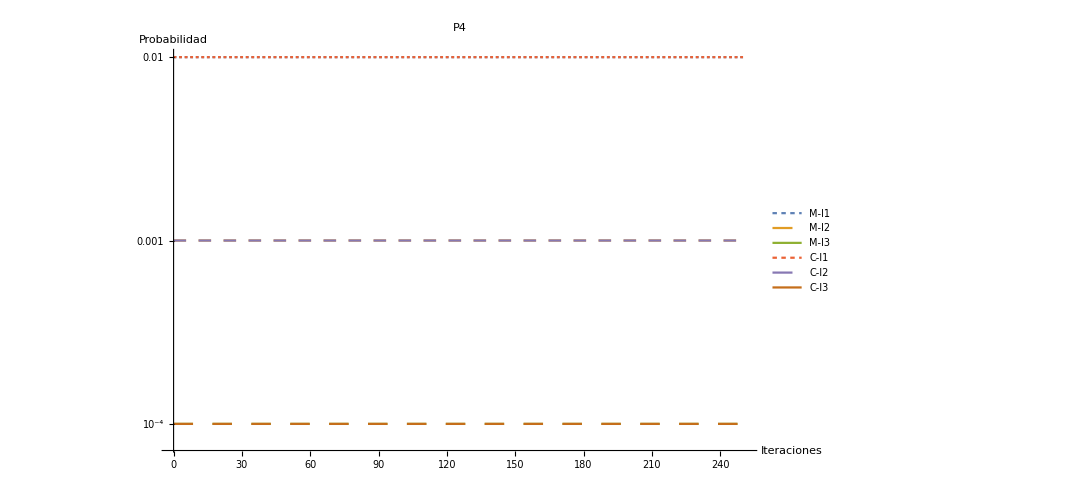
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
y = "/home/fabianact/ActualTesis/Tesis/ModelosPresentados/SinCompetencia";
SetDirectory["/home/fabianact/ActualTesis/Tesis/ModelosPresentados/Curvas/SinCompetencia"];
SetOptions[ListLogPlot,BaseStyle->{FontSize->20}];
pub1= Import[y<>"/averageResults/pub1-0.01-curve.csv"];
pub2= Import[y<>"/averageResults/pub1-0.001-curve.csv"];
pub3= Import[y<>"/averageResults/pub1-1.0E-4-curve.csv"];
pub4 = Import[y<>"/averageResults/pub5-0.01-curve.csv"];
pub5 = Import[y<>"/averageResults/pub5-0.001-curve.csv"];
pub6 = Import[y<>"/averageResults/pub5-1.0E-4-curve.csv"];
plotPub1 = Show[ListLogPlot[{ pub1, pub2, pub3, pub4, pub5, pub6 },ImageSize->800,  AxesLabel->{"Iteraciones","Publicaciones"},Joined->True, PlotLegends->{ "M-I1",  "M-I2", "M-I3",  "C-I1",  "C-I2",  "C-I3"},PlotRange->All,PlotLabel-> "P1",PlotStyle->{Dashing[Tiny],Dashing[Medium], Dashing[Large], Dashing[Tiny], Dashing[Medium], Dashing[Large]}]];

Export["pub-1.png",plotPub1];

pub1= Import[y<>"/averageResults/pub2-0.01-curve.csv"];
pub2= Import[y<>"/averageResults/pub2-0.001-curve.csv"];
pub3= Import[y<>"/averageResults/pub2-1.0E-4-curve.csv"];
pub4 = Import[y<>"/averageResults/pub6-0.01-curve.csv"];
pub5 = Import[y<>"/averageResults/pub6-0.001-curve.csv"];
pub6 = Import[y<>"/averageResults/pub6-1.0E-4-curve.csv"];
plotPub2 = Show[ListLogPlot[{ pub1, pub2, pub3, pub4, pub5, pub6 },ImageSize->800,  AxesLabel->{"Iteraciones","Publicaciones"},Joined->True, PlotLegends->{ "M-I1",  "M-I2", "M-I3",  "C-I1",  "C-I2",  "C-I3"},PlotRange->All,PlotLabel-> "P2", PlotStyle->{Dashing[Tiny],Dashing[Medium], Dashing[Large], Dashing[Tiny], Dashing[Medium], Dashing[Large]}]];
Export["pub-2.png",plotPub2];

pub1= Import[y<>"/averageResults/pub3-0.01-curve.csv"];
pub2= Import[y<>"/averageResults/pub3-0.001-curve.csv"];
pub3= Import[y<>"/averageResults/pub3-1.0E-4-curve.csv"];
pub4 = Import[y<>"/averageResults/pub7-0.01-curve.csv"];
pub5 = Import[y<>"/averageResults/pub7-0.001-curve.csv"];
pub6 = Import[y<>"/averageResults/pub7-1.0E-4-curve.csv"];
plotPub3 = Show[ListLogPlot[{ pub1, pub2, pub3, pub4, pub5, pub6 },ImageSize->800,  AxesLabel->{"Iteraciones","Publicaciones"},Joined->True, PlotLegends->{ "M-I1",  "M-I2", "M-I3",  "C-I1",  "C-I2",  "C-I3"},PlotRange->All,PlotLabel-> "P3",PlotStyle->{Dashing[Tiny],Dashing[Medium], Dashing[Large], Dashing[Tiny], Dashing[Medium], Dashing[Large]}]];
Export["pub-3.png",plotPub3];

pub1= Import[y<>"/averageResults/pub4-0.01-curve.csv"];
pub2= Import[y<>"/averageResults/pub4-0.001-curve.csv"];
pub3= Import[y<>"/averageResults/pub4-1.0E-4-curve.csv"];
pub4 = Import[y<>"/averageResults/pub8-0.01-curve.csv"];
pub5 = Import[y<>"/averageResults/pub8-0.001-curve.csv"];
pub6 = Import[y<>"/averageResults/pub8-1.0E-4-curve.csv"];
plotPub4 = Show[ListLogPlot[{ pub1, pub2, pub3, pub4, pub5, pub6 },ImageSize->800,  AxesLabel->{"Iteraciones","Publicaciones"},Joined->True, PlotLegends->{ "M-I1",  "M-I2", "M-I3",  "C-I1",  "C-I2",  "C-I3"},PlotRange->All,PlotLabel-> "P4",PlotStyle->{Dashing[Tiny],Dashing[Medium], Dashing[Large], Dashing[Tiny], Dashing[Medium], Dashing[Large]}]];
Export["pub-4.png",plotPub4];

pub1= Import[y<>"/averageResults/prob1-0.01-curve.csv"];
pub2= Import[y<>"/averageResults/prob1-0.001-curve.csv"];
pub3= Import[y<>"/averageResults/prob1-1.0E-4-curve.csv"];
pub4 = Import[y<>"/averageResults/prob5-0.01-curve.csv"];
pub5 = Import[y<>"/averageResults/prob5-0.001-curve.csv"];
pub6 = Import[y<>"/averageResults/prob5-1.0E-4-curve.csv"];
plotProb5 = Show[ListLogPlot[{ pub1, pub2, pub3, pub4, pub5, pub6 },ImageSize->800,  AxesLabel->{"Iteraciones","Probabilidad"},Joined->True, PlotLegends->{ "M-I1",  "M-I2", "M-I3",  "C-I1",  "C-I2",  "C-I3"},PlotRange->All,PlotLabel-> "P1",PlotStyle->{Dashing[Tiny],Dashing[Medium], Dashing[Large], Dashing[Tiny], Dashing[Medium], Dashing[Large]}]];

Export["prob-1.png",plotProb5];

pub1= Import[y<>"/averageResults/prob2-0.01-curve.csv"];
pub2= Import[y<>"/averageResults/prob2-0.001-curve.csv"];
pub3= Import[y<>"/averageResults/prob2-1.0E-4-curve.csv"];
pub4 = Import[y<>"/averageResults/prob6-0.01-curve.csv"];
pub5 = Import[y<>"/averageResults/prob6-0.001-curve.csv"];
pub6 = Import[y<>"/averageResults/prob6-1.0E-4-curve.csv"];
plotProb6 = Show[ListLogPlot[{ pub1, pub2, pub3, pub4, pub5, pub6 },ImageSize->800, AxesLabel->{"Iteraciones","Probabilidad"},Joined->True,PlotLegends->{ "M-I1",  "M-I2", "M-I3",  "C-I1",  "C-I2",  "C-I3"},PlotRange->All, PlotLabel-> "P2",PlotStyle->{Dashing[Tiny],Dashing[Medium], Dashing[Large], Dashing[Tiny], Dashing[Medium], Dashing[Large]}]];
Export["prob-2.png",plotProb6];

pub1= Import[y<>"/averageResults/prob3-0.01-curve.csv"];
pub2= Import[y<>"/averageResults/prob3-0.001-curve.csv"];
pub3= Import[y<>"/averageResults/prob3-1.0E-4-curve.csv"];
pub4 = Import[y<>"/averageResults/prob7-0.01-curve.csv"];
pub5 = Import[y<>"/averageResults/prob7-0.001-curve.csv"];
pub6 = Import[y<>"/averageResults/prob7-1.0E-4-curve.csv"];
plotProb7 = Show[ListLogPlot[{ pub1, pub2, pub3, pub4, pub5, pub6 },ImageSize->800, AxesLabel->{"Iteraciones","Probabilidad"},Joined->True, PlotLegends->{ "M-I1",  "M-I2", "M-I3",  "C-I1",  "C-I2",  "C-I3"},PlotRange->All,PlotLabel-> "P3",PlotStyle->{Dashing[Tiny],Dashing[Medium], Dashing[Large], Dashing[Tiny], Dashing[Medium], Dashing[Large]}]];
Export["prob-3.png",plotProb7];

pub1= Import[y<>"/averageResults/prob4-0.01-curve.csv"];
pub2= Import[y<>"/averageResults/prob4-0.001-curve.csv"];
pub3= Import[y<>"/averageResults/prob4-1.0E-4-curve.csv"];
pub4 = Import[y<>"/averageResults/prob8-0.01-curve.csv"];
pub5 = Import[y<>"/averageResults/prob8-0.001-curve.csv"];
pub6 = Import[y<>"/averageResults/prob8-1.0E-4-curve.csv"];
plotProb8 = Show[ListLogPlot[{ pub1, pub2, pub3, pub4, pub5, pub6 },ImageSize->800, AxesLabel->{"Iteraciones","Probabilidad"},Joined->True, PlotLegends->{ "M-I1",  "M-I2", "M-I3",  "C-I1",  "C-I2",  "C-I3"},PlotRange->All, PlotLabel-> "P4",PlotStyle->{Dashing[Tiny],Dashing[Medium], Dashing[Large], Dashing[Tiny], Dashing[Medium], Dashing[Large]}]];
Export["prob-4.png",plotProb8];

pubTotal=Grid[{{plotPub1,plotPub2},{plotPub3,plotPub4}}]
Export["pub-total.png",pubTotal];
probTotal=Grid[{{plotProb5,plotProb6},{plotProb7,plotProb8}}]
Export["prob-total.png",probTotal];
```